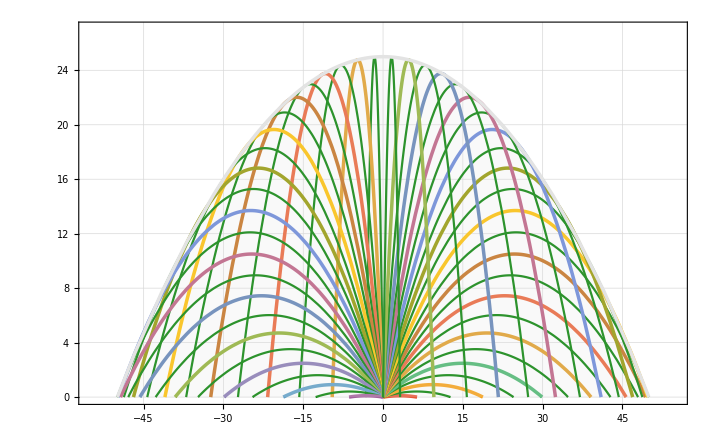

```mathematica
x4=Plot [Evaluate[Table[x Tan[n*π/49]-x^2/((Cos[n*π/49])^2*100),{n,-24,24}]],{x,-120,120},PlotStyle->{RGBColor["Green"],Thickness[0.0035]},FrameStyle->Directive[Black,20],Frame->True,FrameLabel->{Style["",30,Black,FontFamily->"Cambria"],Style["",30,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{-55,55},{0,27}}];
x5=Plot [25-x^2/(100),{x,-120,120},PlotStyle->{RGBColor["#e3e3e3"],Thickness[0.0035]},FrameStyle->Directive[Black,20],Frame->True,FrameLabel->{Style["",30,Black,FontFamily->"Cambria"],Style["",30,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{-55,55},{0,27}}, Filling->Axis];

Show[x4,x5]
```